```mathematica
ComputeProjectionMtx[a_,b_,c_,d_,aPrime_,bPrime_,cPrime_,dPrime_,Oc_,Oc2_]:=Module [{t,M,PM,ProjectionMtxCamera1,ProjectionMtxCamera2},
t:=1/Sqrt[2];
M={{t,0,-t,-6t},{0,1,0,0},{t,0,t,-6t},{0,0,0,1}};
PM={{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};

ProjectionMtxCamera1 = {{zeta1,0,0,0},{0,zeta1,0,0},{0,0,zeta1,0},{0,0,1,0}};
ProjectionMtxCamera2=PM.M;

Print["ProjectionMtxCamera1",MatrixForm[ProjectionMtxCamera1]];
Print["ProjectionMtxCamera2",MatrixForm[ProjectionMtxCamera2]];
ComputeProjectedPointsCamera1And2[ProjectionMtxCamera1,ProjectionMtxCamera2];

];
```

```mathematica
ComputeProjectedPointsCamera1And2[ProjectionMtxCamera1_,ProjectionMtxCamera2_]:=Module[{CameraProjectedPointsK1,CameraProjectedPointsK2,GraphicPointsC1,GraphicPointsC2,G1,G2},

CameraProjectedPointsK1 = Map[ProjectionMtxCamera1.#&,{a,b,c,d,aPrime,bPrime,cPrime,dPrime}];
CameraProjectedPointsK2 = Map[ProjectionMtxCamera2.#&,{a,b,c,d,aPrime,bPrime,cPrime,dPrime}];
Print["CameraProjectedPointsK1 = ", MatrixForm[CameraProjectedPointsK1]];
Print["CameraProjectedPointsK2 = ", MatrixForm[Simplify[CameraProjectedPointsK2]]];

For[i=1,i≤8,i++,
CameraProjectedPointsK1[[i]]=CameraProjectedPointsK1[[i]]/CameraProjectedPointsK1[[i,4]];
CameraProjectedPointsK2[[i]]=CameraProjectedPointsK2[[i]]/CameraProjectedPointsK2[[i,4]];
];

Print["homogene CameraProjectedPointsK1 = ", MatrixForm[CameraProjectedPointsK1]];
Print["homogene CameraProjectedPointsK2 = ", MatrixForm[Simplify[CameraProjectedPointsK2]]];

GraphicPointsC1 = Map[{#[[1]],#[[2]]}&,CameraProjectedPointsK1];
GraphicPointsC2 = Map[{#[[1]],#[[2]]}&,CameraProjectedPointsK2];
G1=ListPlot[GraphicPointsC1[[1;;8]],PlotStyle->Blue];
G2=ListPlot[GraphicPointsC2[[1;;8]],PlotStyle->Red];
Print[Show[G1,G2,PlotRange->All]];
ComputeOrijectedPointsOnImagePlane1And2[CameraProjectedPointsK1,CameraProjectedPointsK2,G1,G2];


];

ComputeOrijectedPointsOnImagePlane1And2[CameraProjectedPointsK1_,CameraProjectedPointsK2_,G1_,G2_]:=Module[{ImagePlaneC1Points,ImagePlaneC2Points},
(*In this case the Image plane Point is equal to the sensor points which is nessecary for the derivation of the fundamental matrix.
-> Take Pitchel pitch of 1 means that only the third element of the Vector is replaced by the forth*)

ImagePlaneC1Points=Map[{#[[1]],#[[2]],#[[4]]}&,CameraProjectedPointsK1 ];
ImagePlaneC2Points=Map[{#[[1]],#[[2]],#[[4]]}&,CameraProjectedPointsK2 ];
Print["ImagePlaneC1Points = ", MatrixForm[Simplify[ImagePlaneC1Points]]];
Print["ImagePlaneC2Points = ", MatrixForm[Simplify[ImagePlaneC2Points]]];

(*If PixelPitch is for example 100 width and 100 height, then it is nessecary to create a new ProjectionMatrix

SensorProjectionMtx = {{-zeta/PixelPitch,0,0},{0,zeta/PixelPitch,0},{0,0,1}}
SensorPoints = SensorProjectionMtx.ImagePlanePoints*)

ComputeFundamentalMatrix[ImagePlaneC1Points,ImagePlaneC2Points,G1,G2];

];

ComputeFundamentalMatrix[ImagePlaneC1Points_,ImagePlaneC2Points_,G1_,G2_]:=Module[{CoefficientMtx,ns,F,lC1,lPrimeC1,lC2,lPrimeC2,RightF,LeftF},
CoefficientMtx = ConstantArray[0,{8,9}];

For[i=1,i≤8,i++,
CoefficientMtx[[i]]=
{ImagePlaneC2Points[[i,1]]*ImagePlaneC1Points[[i,1]],ImagePlaneC2Points[[i,1]]*ImagePlaneC1Points[[i,2]],ImagePlaneC2Points[[i,1]],ImagePlaneC2Points[[i,2]]*ImagePlaneC1Points[[i,1]],ImagePlaneC2Points[[i,2]]*ImagePlaneC1Points[[i,2]],ImagePlaneC2Points[[i,2]],ImagePlaneC1Points[[i,1]],ImagePlaneC1Points[[i,2]],1};
];

Print["CoefficientMtx = ", MatrixForm[Simplify[CoefficientMtx]]];
Print["RowReduce CoefficientMtx = "[MatrixForm[RowReduce[Simplify[CoefficientMtx]]]]];

Flatten[ns=NullSpace[Simplify[CoefficientMtx]]];
(*ns=Flatten[ns];*)

Print["ns =", ns];

F={{ns[[1,1]],ns[[1,2]],ns[[1,3]]},{ns[[1,4]],ns[[1,5]],ns[[1,6]]},{ns[[1,7]],ns[[1,8]],ns[[1,9]]}};

Print["F = ", MatrixForm[F]];

lC1=ConstantArray[0,{8,3}];
lPrimeC1=ConstantArray[0,{8,3}];

(*lPrimeC1 = F.ImagePlaneC2Points;*)

For[i=1,i≤8,i++,
lC1[[i]]=Simplify[F.ImagePlaneC1Points[[i,All]]];
lPrimeC1[[i]] = Simplify[Transpose[F].ImagePlaneC2Points[[i,All]]]
];
Print["lC1 = ", lC1];
Print["lPrimeC1 = ", lPrimeC1];
RightF=Flatten[ NullSpace[F]];
LeftF=Flatten[NullSpace[Transpose[F]]];

Print["e = ", RightF];
Print["e' = ", LeftF];

Print[Show[G2,ContourPlot[lC1[[1]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[2]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[3]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[4]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[5]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[6]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[7]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lC1[[8]].{x,y,1}==0,{x,-3,3},{y,-3,3}],G1,ContourPlot[lPrimeC1[[1]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[2]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[3]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[4]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[5]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[6]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[7]].{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lPrimeC1[[8]].{x,y,1}==0,{x,-3,3},{y,-3,3}],PlotRange->All]];


];
```

```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,8,-6,1};
Oc={0,0,0,1};
Oc2={6,0,0,1};
zeta1 = -2;
```

ProjectionMtxCamera1(-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(-1/(√2) | 0 | 1/(√2) | 3 √2
0 | -1 | 0 | 0
-1/(√2) | 0 | -1/(√2) | 3 √2
1/(√2) | 0 | 1/(√2) | -3 √2)

CameraProjectedPointsK1 = (-6 | -6 | 8 | -4
-10 | -6 | 8 | -4
-10 | -10 | 8 | -4
-6 | -10 | 8 | -4
-6 | -6 | 12 | -6
-10 | -6 | 12 | -6
-10 | -10 | 12 | -6
-6 | -16 | 12 | -6)

CameraProjectedPointsK2 = (-1/(√2) | -3 | 7/(√2) | -7/(√2)
-3/(√2) | -3 | 5/(√2) | -5/(√2)
-3/(√2) | -5 | 5/(√2) | -5/(√2)
-1/(√2) | -5 | 7/(√2) | -7/(√2)
-3/(√2) | -3 | 9/(√2) | -9/(√2)
-5/(√2) | -3 | 7/(√2) | -7/(√2)
-5/(√2) | -5 | 7/(√2) | -7/(√2)
-3/(√2) | -8 | 9/(√2) | -9/(√2))

homogene CameraProjectedPointsK1 = (3/2 | 3/2 | -2 | 1
5/2 | 3/2 | -2 | 1
5/2 | 5/2 | -2 | 1
3/2 | 5/2 | -2 | 1
1 | 1 | -2 | 1
5/3 | 1 | -2 | 1
5/3 | 5/3 | -2 | 1
1 | 8/3 | -2 | 1)

homogene CameraProjectedPointsK2 = (1/7 | (3 √2)/7 | -1 | 1
3/5 | (3 √2)/5 | -1 | 1
3/5 | √2 | -1 | 1
1/7 | (5 √2)/7 | -1 | 1
1/3 | (√2)/3 | -1 | 1
5/7 | (3 √2)/7 | -1 | 1
5/7 | (5 √2)/7 | -1 | 1
1/3 | (8 √2)/9 | -1 | 1)

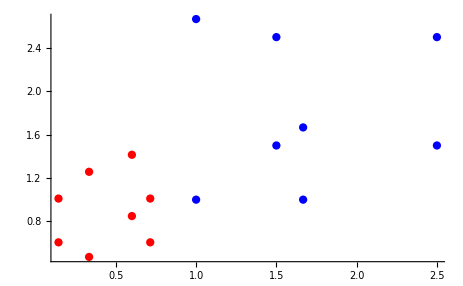

ImagePlaneC1Points = (3/2 | 3/2 | 1
5/2 | 3/2 | 1
5/2 | 5/2 | 1
3/2 | 5/2 | 1
1 | 1 | 1
5/3 | 1 | 1
5/3 | 5/3 | 1
1 | 8/3 | 1)

ImagePlaneC2Points = (1/7 | (3 √2)/7 | 1
3/5 | (3 √2)/5 | 1
3/5 | √2 | 1
1/7 | (5 √2)/7 | 1
1/3 | (√2)/3 | 1
5/7 | (3 √2)/7 | 1
5/7 | (5 √2)/7 | 1
1/3 | (8 √2)/9 | 1)

CoefficientMtx = (3/14 | 3/14 | 1/7 | 9/(7 √2) | 9/(7 √2) | (3 √2)/7 | 3/2 | 3/2 | 1
3/2 | 9/10 | 3/5 | 3/(√2) | 9/(5 √2) | (3 √2)/5 | 5/2 | 3/2 | 1
3/2 | 3/2 | 3/5 | 5/(√2) | 5/(√2) | √2 | 5/2 | 5/2 | 1
3/14 | 5/14 | 1/7 | 15/(7 √2) | 25/(7 √2) | (5 √2)/7 | 3/2 | 5/2 | 1
1/3 | 1/3 | 1/3 | (√2)/3 | (√2)/3 | (√2)/3 | 1 | 1 | 1
25/21 | 5/7 | 5/7 | (5 √2)/7 | (3 √2)/7 | (3 √2)/7 | 5/3 | 1 | 1
25/21 | 25/21 | 5/7 | (25 √2)/21 | (25 √2)/21 | (5 √2)/7 | 5/3 | 5/3 | 1
1/3 | 8/9 | 1/3 | (8 √2)/9 | (64 √2)/27 | (8 √2)/9 | 1 | 8/3 | 1)

RowReduce CoefficientMtx = [(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)]

ns ={{0,1,0,0,0,-2 √2,0,1,0}}

F = (0 | 1 | 0
0 | 0 | -2 √2
0 | 1 | 0)

lC1 = {{3/2,-2 √2,3/2},{3/2,-2 √2,3/2},{5/2,-2 √2,5/2},{5/2,-2 √2,5/2},{1,-2 √2,1},{1,-2 √2,1},{5/3,-2 √2,5/3},{8/3,-2 √2,8/3}}

lPrimeC1 = {{0,8/7,-12/7},{0,8/5,-12/5},{0,8/5,-4},{0,8/7,-20/7},{0,4/3,-4/3},{0,12/7,-12/7},{0,12/7,-20/7},{0,4/3,-32/9}}

e = {1,0,0}

e' = {-1,0,1}

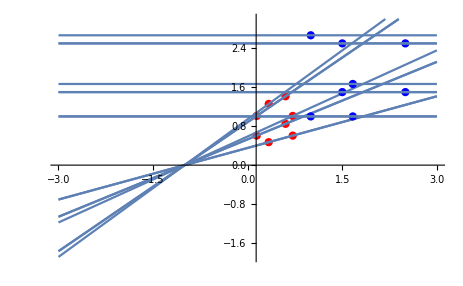

```mathematica
ComputeProjectionMtx[a,b,c,d,aPrime,bPrime,cPrime,dPrime,Oc,Oc2];
```